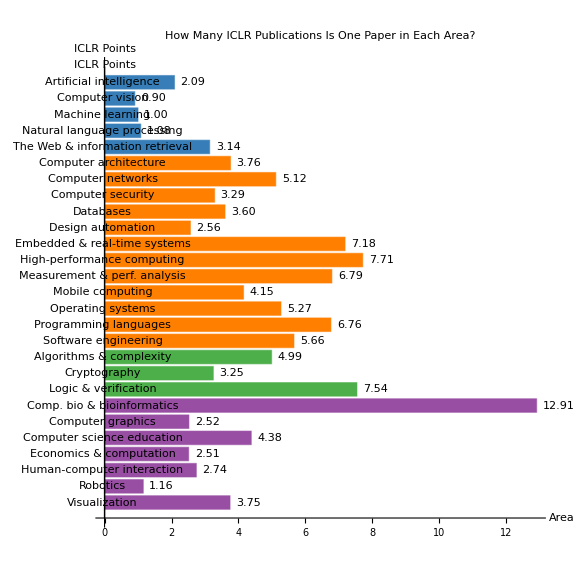

```mathematica
(*Import names.csv and build a mapping:ParentArea->{ReadableTitle,ParentParentArea}*)namesData=Import[FileNameJoin[{NotebookDirectory[],"names.csv"}],"CSV"];
namesData=Rest[namesData];  (*remove header row*)
areaMapping=Association[Table[namesData[[i,1]]->{namesData[[i,2]],namesData[[i,3]]},{i,Length[namesData]}]];

(*Import the publication data*)
data=Import[FileNameJoin[{NotebookDirectory[],"pubs_per_faculty_with_iclr.csv"}],"CSV"];
data=Rest[data];  (*remove header row*)
areas=data[[All,1]];
iclrPoints=ToExpression[data[[All,5]]];

(*Map each ParentArea to its readable title and parent parent area*)
mapped=areaMapping/@areas;
readableTitles=mapped[[All,1]];
parentParent=mapped[[All,2]];

(*Define a unique color for each ParentParentArea*)
colorMapping=<|"AI"->RGBColor[55/255,126/255,184/255],"Systems"->RGBColor[255/255,127/255,0/255],"Theory"->RGBColor[77/255,175/255,74/255],"Interdisciplinary Areas"->RGBColor[152/255,78/255,163/255]|>;
barColors=Lookup[colorMapping,parentParent,Gray];

(*Define desired order for ParentParentArea*)
order={"AI","Systems","Theory","Interdisciplinary Areas"};
sortKey[pp_]:=FirstPosition[order,pp,{Infinity}][[1]];

(*Combine and sort the data based on ParentParentArea order*)
combined=Transpose[{readableTitles,iclrPoints,parentParent,barColors}];
sortedCombined=SortBy[combined,sortKey[#[[3]]]&];
sortedReadable=sortedCombined[[All,1]];
sortedICLRPoints=sortedCombined[[All,2]];
sortedBarColors=sortedCombined[[All,4]];

(*Create a horizontal bar chart*)
BarChart[Reverse@sortedICLRPoints,LabelingFunction->(Placed[NumberForm[#1,{4,2}],After]&),AspectRatio->1,BarOrigin->Left,ChartLabels->Reverse@sortedReadable,ChartStyle->Reverse@sortedBarColors,AxesLabel->{"ICLR Points","Area"},PlotLabel->"How Many ICLR Publications Is One Paper in Each Area?",ImageSize->Large]
```